# RGErun 2.2.3

```mathematica
Quit[];
```

Author: Kristjan Kannike. Created: 2004-08-07. Changed: 2017-12-13.
Available under the GNU General Public Licence <http://www.gnu.org/copyleft/gpl.html>.
General framework for running renormalisation group equations.

## The RGErun Package

```mathematica
BeginPackage["RGErun`"];
```

Preamble

```mathematica
β::usage="β[x,model,thresholds] is used to enter the beta function for the variable x in the model; the beta function may depend the thresholds below the current energy scale if different effective field theories are used; if not, you can set it to _.";
```

```mathematica
run::usage="run[thresholds,variables,direction,model] runs the RGEs between thresholds in the direction (up or down), gives variables as functions of the energy scale and optionally matches variables at thresholds or prints out the values of the variables and their predefined functions at the thresholds together with a plot of running couplings.";
```

```mathematica
printOut::usage="printOut is an option for run which specifies whether the results and matched results at each scale should be printed out together with a plot of the running variables; the default value is printOut → True";
```

```mathematica
matches::usage="matches is an option for run which specifies the matching conditions for the running variables at thresholds.";
```

```mathematica
functions::usage="functions is an option for run which specifies functions of the running variables (e.g. eigenvalues of a mass matrix) that should be printed out at thresholds.";
```

```mathematica
𝕀::usage="𝕀 must be used in lieu of IdentityMatrix[n] in the beta functions.";
```

```mathematica
CirclePlus::usage="Use ⊕ instead of + to add a constant vector or matrix in a beta function.";
```

```mathematica
CircleTimes::usage="Use ⊗ instead of * to multiply element-wise by constant vector or matrix in a beta function.";
```

```mathematica
getRGEs::usage="getRGEs[name] imports the β-functions defined in the output of SARAH (name is the directory of SARAH output) or PyR@TE (name is the file with PyR@TE Mathematica output).";
```

```mathematica
returnVariables::usage="returnVariables is an option for getRGEs that specifies whether to return a list of variables defined in a PyR@TE Mathematica output.";
replaceNames::usage="replaceNames is an option for getRGEs to replace variable names defined in the PyR@TE output.";
```

```mathematica
updateInstalled::usage="updateInstalled[directory] replaces the RGErun.m package in the user's Mathematica Applications folder with the one in the directory (the default is NotebookDirectory[]).";
```

```mathematica
Options[getRGEs]={returnVariables->False,replaceNames->{}};
getRGEs[name_:"",model_:"",OptionsPattern[]]:=Block[{variableSubs,AllRGEs,DimensionParameter,conj,Tp,Adj,trace,MatMul,pi},
Which[name==""&&And@@Map[Head[#]===List&,{BetaGauge,BetaLijkl,BetaYijk,BetaTijk,BetaMuij,BetaBij,BetaVEV}],(* SARAH definitions in the Global context *)
AllRGEs=
Join[BetaGauge,BetaLijkl,BetaYijk,BetaTijk,BetaMuij,BetaBij,BetaVEV],
DirectoryQ[name],(* Directory with SARAH output *)
AllRGEs=Flatten[Get[FileNameJoin[{name,#}]]&/@{"BetaGauge.m","BetaLijkl.m","BetaYijk.m","BetaTijk.m","BetaMuij.m","BetaBij.m","BetaVEV.m"},1],
True,(* PyR@TE output file *)
AllRGEs=Get[name]
];
If[Last[Dimensions[AllRGEs]]==3,(* Convert from SARAH format *){First[#],{1/(16 π^2),(1/(16 π^2))^2}.Rest[#]}&/@AllRGEs];
variableSubs=Map[#->Head[#]&,Select[AllRGEs⟦All,1⟧,!AtomQ[#]&]];Scan[(β[First[#],model,_]:=Last[#])&,AllRGEs/.pi->π/.variableSubs/.OptionValue[replaceNames]//.{conj->Conjugate,Tp->Transpose,Adj->ConjugateTranspose,trace[ms__]:>Tr[Dot[ms]],MatMul[ms__][__]:>Dot[ms]}];
If[OptionValue[returnVariables]==True,AllRGEs⟦All,1⟧/.variableSubs/.OptionValue[replaceNames]]
];
```

```mathematica
updateInstalled[directory_:NotebookDirectory[]]:=Block[{newVersion=FileNameJoin[{directory,"RGErun.m"}],
installedVersion=FileNameJoin[{$UserBaseDirectory,"Applications","RGErun.m"}]},
If[FileExistsQ[newVersion],
If[FileExistsQ[installedVersion],DeleteFile[installedVersion]];
CopyFile[newVersion,installedVersion];
Print[StringForm["Copied `1` to `2`.",newVersion,installedVersion]],
Print["No RGErun.m in ",directory]];
];
```

```mathematica
Begin["`Private`"];
```

Auxiliary Constants & Functions

```mathematica
SetAttributes[{𝕀},Protected];
SetAttributes[{CirclePlus,CircleTimes},{HoldAll,Protected}];
chopδ=0 10^-20;
```

```mathematica
numericQ::usage="numericQ[expr] returns True if expr is a numeric quantity or a full array of numeric quantities and False otherwise.";
numericQ[x_]:=NumericQ[x]||ArrayQ[x,_,NumericQ];
```

```mathematica
flatten::usage="flatten[x] flattens x if x is a list, else returns {x}.";
flatten[xs_]:=If[Dimensions[N[xs]]=={},{xs},Flatten[xs]];
```

```mathematica
threadEqual::usage="threadEqual[xs,ys] returns equations formed from flatten'ed xs and ys";
threadEqual[xs_,ys_]:=Thread[flatten[xs]==flatten[ys]];
```

```mathematica
numericsNamesQ::usage="numericsNamesQ[variables,scale] returns the list of variables that are numeric at the scale.";
numericAtScaleQ[variables_,scale_]:=Select[variables,numericQ[#[scale]]&];
```

```mathematica
complexInterpolationFunctionQ::usage="complexInterpolationFunctionQ[if] returns True if the InterpolationFunction is complex anywhere and False otherwise.";
complexInterpolationFunctionQ[if_]:=Cases[Chop[Im[if⟦4,3⟧]],Except[0|0.]]≠{};
```

```mathematica
split::usage="Split a list into parts such that the length of each part is given by the second argument.";
split[list_,parts_]:=Map[Take[list,#1+{1,0}]&,Partition[FoldList[Plus,0,parts],2,1]];
(* Taken from Programming With Mathematica, An Introduction by Paul Wellin *)
```

```mathematica
printSeparator::usage="printSeparator[n] prints a row of n —'s";
printSeparator[n_:50,c_:"—"]:=Print[StringJoin[ConstantArray[c,n]]];
```

```mathematica
style::usage="style[text,name] sets the text to a predefined style.";
style[text_,"header"]:=Style[text,FontSize->16];
```

```mathematica
display::usage="display[variable] returns the variable in MatrixForm if the variable is a vector or matrix, otherwise it returns the variable";
display[variable_]:=If[ArrayQ[variable],MatrixForm[Chop[N[variable],chopδ]],Chop[N[variable],chopδ]];
```

```mathematica
printIntermediateResults::usage="printIntermediateResults[thresholds, scale, variables, functions,done] prints out intermediate results in runup if printOut→True; done specifies whether the variables are \"Run\" etc.";
printIntermediateResults[thresholds_,scale_,variables_,functions_,done_:"Run",unit_:"GeV"]:=Block[{},
Print["Results @ "<>StringJoin[Riffle[thresholds," = "]]<>" = ",N[scale]," ",unit];
Print[done<>" variables:"];
Print[Sequence@@Flatten[Riffle[{ToString[#]," = ",display[#[scale]]}&/@variables,
", "]]];
If[functions≠{},
Print[done<>" functions:"];
Print[Sequence@@Flatten[Riffle[{ToString[#]," = ",display[#[scale]]}&/@functions,
", "]]];
];
];
```

```mathematica
checkInitialConditions::usage="checkInitialConditions[variables] checks whether all the initial conditions to run are defined and numerical at the scale.";
checkInitialConditions[variables_,scale_]:=With[{numerics=numericAtScaleQ[variables,scale]},If[numerics≠variables,Message[run::nonnum,ToString/@Complement[variables,numerics]]];
Complement[variables,numerics]];
```

```mathematica
groupThresholds::usage="groupThresholds[thresholds] takes as arguments the list of \"threshold name\" → scale rules and returns the {sorted names, sorted mass scales} list.";
groupThresholds[thresholds_]:=Block[{thrs=GatherBy[SortBy[thresholds,Last],Last]},
{Map[First,thrs,{2}],Map[Last@First[#]&,thrs]}
];
```

```mathematica
ts::usage="ts[massScales] returns logs of ratios of mass levels from a vector.";
ts[massScales_]:={Log[#1/#2],10^-30}&@@@Partition[massScales,2,1];(* The value 10^-30 instead of 0 as an upper bound avoids an NDSolve bug in v. 10.1 *)
```

```mathematica
runBetweenThresholds::usage="runBetweenThresholds[scale,tMin,tMax,thresholds,variables], where the initial values for the variables must be given at scale, solves the equations in the interval from tMin to tMax.";
runBetweenThresholds[scale_,tMin_,tMax_,model_,thresholds_,variables_,opts:OptionsPattern[]]:=Block[{eqs,vars,sub,t},
sub=
ReleaseHold[With[{name=Symbol[ToString[#]<>"$"]},Hold[Sequence[#'[t]->Array[name[##]'[t]&,Dimensions[N[#[scale]]]],#->
Array[name[##][t]&,Dimensions[N[#[scale]]]]]]]&/@variables];
eqs=Flatten[ReleaseHold[Hold@Sequence[
threadEqual[#'[t]/.sub/.𝕀:>IdentityMatrix[First[Dimensions[N[#[scale]]]]],β[#,model,thresholds]/.sub/.𝕀:>IdentityMatrix[First[Dimensions[N[#[scale]]]]]/.{CirclePlus->Plus,CircleTimes->Times}],threadEqual[#/.sub/.t->tMin,#[scale]]]&/@variables]];
vars=Flatten[With[{name=Symbol[ToString[#]<>"$"]},Array[name[##]&,Dimensions[N[#[scale]]]]]&/@variables];
First[NDSolve[eqs,vars,{t,tMin,tMax},FilterRules[{opts},Options[NDSolve]]]]
];
```

```mathematica
pieceTogether::usage="pieceTogether[variables,solutions,scales] pieces together each variable and its Derivatives as a function of the renormalisation scale from the solutions to the RGEs.";
pieceTogether[variables_,solutions_,scales_,model_]:=(
Scan[
(#[μ_?NumericQ,model]:=Block[{intervals=Interval/@Partition[scales,2,1]},
Piecewise[
With[{var=#,varS=Symbol[ToString[#]<>"$"]},
MapThread[{
 Hold[(* To avoid evaluation of functions in wrong intervals *)
With[{scale=#2⟦1,2⟧},
Array[
varS[##][Log[μ]-Log[scale]]&,
Dimensions[N[var[scales⟦1⟧]]]
]
]/.#1
],
IntervalMemberQ[#2,μ]
}&,
{solutions,intervals}]],
Which[μ<scales⟦1⟧,#[scales⟦1⟧],μ>scales⟦-1⟧,#[scales⟦-1⟧]]]//ReleaseHold
];
#[μ_?NumericQ]:=Evaluate[#][μ,model];
)&,
variables];
Scan[
(Derivative[n_][#][μ_?NumericQ,model]:=Block[{intervals=Interval/@Partition[scales,2,1]},
Piecewise[
With[{var=#,varS=Symbol[ToString[#]<>"$"]},
MapThread[{
 Hold[(* To avoid evaluation of functions in wrong intervals *)
With[{scale=#2⟦1,2⟧},
Array[
1/μ^n StirlingS1[n,Range[n]].With[{is=##},Derivative[#][varS[is]][Log[μ]-Log[scale]]&/@Range[n]]&,
Dimensions[N[var[scales⟦1⟧]]]
]
]/.#1
],
IntervalMemberQ[#2,μ]
}&,
{solutions,intervals}]],
Array[0&,Dimensions[N[#[scales⟦1⟧]]]]]//ReleaseHold
];
Derivative[n_][#][μ_?NumericQ]:=Derivative[n][Evaluate[#]][μ,model];
)&,
variables];
);
```

Run & Display

```mathematica
plotStyles={Black,ColorData["Legacy"]["LightCadmiumRed"],ColorData["Legacy"]["PermanentGreen"],ColorData["Crayola"]["Blue"],ColorData["Legacy"]["Apricot"],ColorData["Legacy"]["BlueViolet"],ColorData["Legacy"]["Gold"],Black};
```

```mathematica
(*optimalPosition::usage="optimalPosition[variables,minX,maxX] gives the rough position between minX and maxX where the variables are most distant from each other.";optimalPosition[variables_,areComplexes_,minX_,maxX_]:=Block[{dist},
dist[list_]:=Total[Abs[Subtract@@#]&/@Subsets[list,{2}]];
SortBy[Block[{x=#},{x,dist[Flatten@MapThread[If[And@@#2==False,#1[x],ReIm[#1[x]]]&,{variables,areComplexes}]]}]&/@Rest[Most[Exp[Subdivide[Log[minX],Log[maxX],10]]]],Last]⟦-1,1⟧
]*)
```

```mathematica
SetAttributes[{printOut},Protected];
Options[run]={printOut->True,matches->{},functions->{}}~Join~Options[NDSolve];
run::nonnum="The initial condition(s) for `1` is/are not numerical and/or not full arrays.";
run[thresholds_,variables_,direction_:"up",model_:"",opts:OptionsPattern[]]:=Block[{dir=Which[direction=="up",1,direction=="down",-1],thrs,scales,intervals,t,thr,runthr,matchedHere,runBetween,piecewiseVariables,areComplexes,normalThresholds=Normal[thresholds](*,position*)},
{thrs,scales}=groupThresholds[normalThresholds];
intervals=Partition[scales,2,1];
intervals=Which[direction=="up",intervals,direction=="down",Reverse[intervals]];
Evaluate[thr/@scales]=thrs;
Evaluate[runthr/@scales]=FoldList[Join,First[thrs],Rest[thrs]];
(* Since there is no running at the first scale, it is undefined *)
Evaluate[t/@Which[direction=="up",Rest[scales],direction=="down",Most[scales]]]=ts[scales];
(* Run in each interval and print out results *)
runBetween=Block[{tMin,tMax,int=#2,runVariables},
If[checkInitialConditions[variables,int⟦dir⟧]=={},
{tMin,tMax}={t[int⟦-dir⟧]⟦dir⟧,t[int⟦-dir⟧]⟦-dir⟧} ;
runVariables=runBetweenThresholds[int⟦dir⟧,tMin,tMax,model,runthr[int⟦dir⟧],variables,FilterRules[{opts},Options[NDSolve]]];
Scan[(#[int⟦-dir⟧]=With[{name=Symbol[ToString[#]<>"$"]},Array[name[##][tMax]&,Dimensions[N[#[scales⟦dir⟧]]]]]/.runVariables)&,variables];
If[OptionValue[printOut]==True,printSeparator[];
printIntermediateResults[thr[int⟦-dir⟧],int⟦-dir⟧,variables,OptionValue[functions]]];
matchedHere={};

Scan[Module[{mtch=#⟦2⟧[model,int⟦-dir⟧,thr[int⟦-dir⟧],direction]},
If[numericQ[mtch],#⟦1⟧[int⟦-dir⟧]=mtch;AppendTo[matchedHere,#⟦1⟧]]]&,OptionValue[matches]];


If[OptionValue[printOut]==True&&matchedHere≠{},printIntermediateResults[thr[int⟦-dir⟧],int⟦-dir⟧,matchedHere,OptionValue[functions],"Matched"];
printSeparator[]];
Append[#1,runVariables]
]
]&;

(* Do not evaluate anything if some initial conditions are ill defined: *)
If[checkInitialConditions[variables,scales⟦dir⟧]=={},
If[OptionValue[printOut]==True,
printSeparator[];
Print["RUNNING "<>ToUpperCase[direction]<>" IN MODEL "<>model];
 ];
If[OptionValue[printOut]==True,printIntermediateResults[thr[scales⟦dir⟧],scales⟦dir⟧,variables,OptionValue[functions],"Initial"]];
piecewiseVariables=Fold[runBetween,{},intervals];
If[OptionValue[printOut]==True,
printSeparator[]
 ];
If[direction=="down",piecewiseVariables=Reverse[piecewiseVariables]];

pieceTogether[variables,piecewiseVariables,scales,model];

(* Which variables have complex values? *)
areComplexes=Map[Or@@Map[complexInterpolationFunctionQ[Last[#]]&,#]&,Transpose[piecewiseVariables]];
areComplexes=split[areComplexes,Times@@Dimensions[#[scales⟦1⟧]]&/@variables];


If[OptionValue[printOut]==True&&checkInitialConditions[variables,scales⟦-dir⟧]=={},
(* Show a plot with all the running variables *)

(* Calculate the optimal position(s) for the labels *)
(*positions=Log[optimalPosition[variables,areComplexes,scales⟦1⟧,scales⟦-1⟧]];*)
(*positions=optimalPositions[fs_,{{xMin_,xMax_},{yMin_,yMax_}}];*)

Print[
Show[Reverse@Sort@Flatten@MapThread[
Block[{variable=#1,areComplex=#2,colour=#3,position=RandomReal[Log[scales⟦{1,-1}⟧]],dimensions=Dimensions[N[#1[scales⟦1⟧]]],indices},
indices=If[dimensions=={},{""},Flatten[Array[Style[StringJoin[Riffle[ToString/@{##},","]],Red]&,dimensions]]];
MapIndexed[
{
LogLinearPlot[
With[{vari=flatten[variable[μ]]⟦Sequence@@#2⟧},If[#1,{Re[vari],Im[vari]},vari]],{μ,scales⟦1⟧,scales⟦-1⟧},AxesLabel->{"μ/GeV",""},AxesOrigin->{scales⟦1⟧,0},PlotStyle->colour,PlotRange->All,Method->{"AxesInFront"->False}],
Block[{index=#2},With[{vari=flatten[variable[ⅇ^position]]⟦Sequence@@index⟧,ind=indices⟦Sequence@@index⟧},
Graphics[Text[If[dimensions=={},First[#],Subscript[First[#],ind]],{position,Last[#]},Background->White]]&/@If[#1,{{StringForm["Re ``",variable],Re[vari]},{StringForm["Im ``",variable],Im[vari]}},{{ToString[variable],vari}}]]
]
}&,
areComplex]
]&,
{variables,areComplexes,Flatten[ConstantArray[plotStyles,Quotient[Length[variables],Length[plotStyles]]]]~Join~Take[plotStyles,Length[variables]~Mod~Length[plotStyles]]}
],
PlotRange->All]
];
printSeparator[]
 ];
];
];
```

```mathematica
End[];
```

```mathematica
EndPackage[];
```

Change Log

TO DO: Switching RGEs not only by switching scales, but also models (splice together running variables of different models). Or: switching models at scales: a model or an EFT is defined between two scales. Because usually the RGEs for different EFTs are calculated separately and splicing them together is extra effort/source of error.
Instead of thresholds, models??
Model can be valid from 0... m1, m1...m2, m2...∞. In case of ∞, run up to the Planck mass.

2017-12-13: 2.2.3: Bug fix: matching work with new “up” and “down”.
2017-07-31: 2.2.2: Added model as an optional argument to variables; if two models “1” and “2” have a λ, then λ[μ] will equal the last evaluated of λ[μ,"1"] and λ[μ,"2"].
2017-07-30: 2.2.1: 𝕀 does not need an explicit argument anymore: where it is used, the variable is assumed to be a square matrix so 𝕀 gets first of its dimensions.
2016-09-01: 2.2.0:  Changed up and down to strings “up” and “down”.
2016-04-12: 2.1.9: Below the lowest or the highest scale, any variable now has the constant value at that scale and its derivative is zero.
2015-06-04: 2.1.8: Updated usage messages for run and β.
2015-05-29: 2.1.7: Changed getRGEs to read in β-functions from the Mathematica output of the SARAH package.
2015-05-28: 2.1.6: Renamed getPyRATERGEs to getRGEs.
2015-05-19: 2.1.5: Added model as an argument to run, β, match and getRGEs.
2015-05-19: 2.1.4: Changed matches and functions from arguments to run to its options.
2015-05-19: 2.1.3: Changed the format of β-functions: instead of β[λ][t,thresholds] it is β[λ,model,thresholds].
2015-05-18: 2.1.2: Put the code that updates the package in the Mathematica Applications directory in the updateInstalled function.
2015-05-18: 2.1.1: Changed the name of getPyrateRGEs into getPyRATERGEs to conform with the official name of that package.
2015-05-18: 2.1.0: Avoid an NDSolve bug in Mathematica 10.1: set t_max=10^-30 instead of t_max=0 in the ts function.
2015-05-15: 2.0.9: Thresholds can now be entered as an Association.
2015-04-08: 2.0.8: Updated to the look of Mathematica 10.
2014-07-27: 2.0.7: Bug fix: made plotting Re and Im parts more robust; added Method→{"AxesInFront"→False}.
2014-07-27: 2.0.6: Added getPyrateRGEs to read in and convert β-functions from the Mathematica output of the PyR@TE package.
2014-07-26: 2.0.5: Bug fix: converted the cells of the usage messages of 𝕀, CirclePlus and CircleTimes into initialization cells.
2014-06-18: 2.0.4: Plotting the real and imaginary part of complex couplings.
2014-06-18: 2.0.3: All order derivatives of running couplings.
2013-10-03: 2.0.2: Removed the the maxSteps and workPrecision options to run and made it accept the Options of NDSolve.
2013-10-02: 2.0.1:  Bug fix: changed everywhere Dimensions[…] to Dimensions[N[…]] to ensure that a scalar with an exact initial condition such as π/2 is internally treated as a scalar.

## Examples

You can copy the package RGErun.m from the current directory to your Mathematica Applications directory (evaluate ‘The RGErun Package’ section above first):

```mathematica
updateInstalled[]
```

Copied /Users/kristjan/Documents/html_doc/HTML5/english/science/physics/RGE_run_EFT/code/RGErun.m to /Users/kristjan/Library/Mathematica/Applications/RGErun.m.

Read in the package:

```mathematica
Needs["RGErun`"];
```

```mathematica
?run
```

run[thresholds,variables,direction,model] runs the RGEs between thresholds in the direction (up or down), gives variables as functions of the energy scale and optionally matches variables at thresholds or prints out the values of the variables and their predefined functions at the thresholds together with a plot of running couplings.

Running of the Gauge Couplings, the Higgs λ and y_t in the Standard Model

The RGes of the gauge couplings and y_t are at 2-loop level. For simplicity, the RGE for λ is at 1-loop level, as it makes little numerical difference. Notice that run accepts all the options of NDSolve.

——————————————————————————————————————————————————

RUNNING UP IN MODEL SM

Results @ m_t = 173.34 GeV

Initial variables:

g1 = 0.463983, g2 = 0.64754, g3 = 1.1666, yt = 0.95096, λ = 0.12879

——————————————————————————————————————————————————

Results @ TeV = 1000. GeV

Run variables:

g1 = 0.468679, g2 = 0.638499, g3 = 1.05728, yt = 0.869635, λ = 0.0966375

——————————————————————————————————————————————————

Results @ m_P = 1.22×10^19 GeV

Run variables:

g1 = 0.618675, g2 = 0.505272, g3 = 0.487305, yt = 0.395522, λ = -0.0172939

——————————————————————————————————————————————————

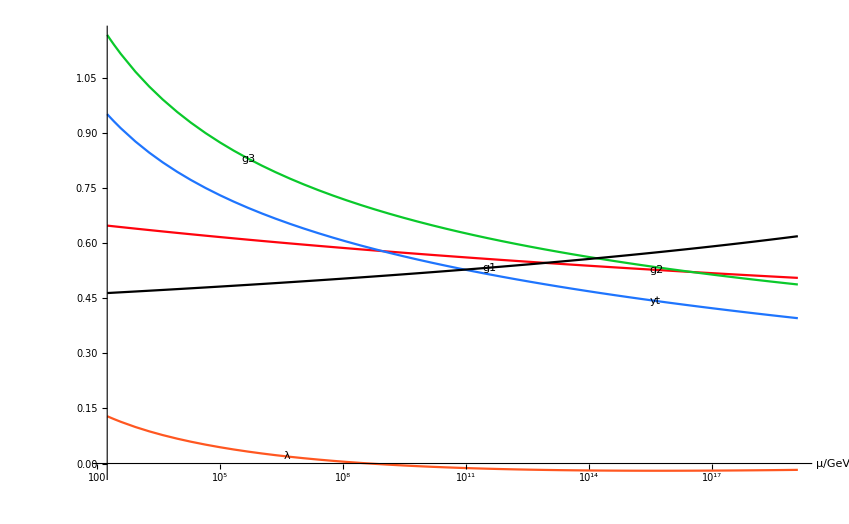

——————————————————————————————————————————————————

```mathematica
mt=173.34;mP=1.22 10^19;mHi=10^20 mP;
thresholds={"m_t"->mt,"TeV"->1000,"m_P"->mP};
variables={g1,g2,g3,yt,λ};
g1[mt]=√(5/3) 0.35940;
g2[mt]=0.64754;
g3[mt]=1.1666;
yt[mt]=0.95096;
λ[mt]=0.12879;

β[g1,"SM",_]:=1/(16 π^2)41/10 g1^3+(1/(16 π^2))^2 g1^3 (44/5 g3^2+27/10 g2^2+199/50 g1^2-17/10 yt^2);

β[g2,"SM",_]:=1/(16 π^2)(-19/6) g2^3+(1/(16 π^2))^2 g2^3(12 g3^2+35/6 g2^2+9/10 g1^2-3/2 yt^2);

β[g3,"SM",_]:=1/(16 π^2)(-7)g3^3+(1/(16 π^2))^2 g3^3 (-26 g3^2+9/2 g2^2+11/10 g1^2-2 yt^2);

β[yt,"SM",_]:=1/(16 π^2) (9/2 yt^2-17/20 g1^2-9/4 g2^2-8 g3^2) yt+(1/(16 π^2))^2  yt (yt^2 (-12 yt^2-12 λ+36 g3^2+225/16 g2^2+393/80 g1^2)+6 λ^2-108 g3^4-23/4 g2^4+1187/600 g1^4+9 g2^2 g3^2+19/15 g1^2 g3^2-9/20 g1^2 g2^2);

β[λ,"SM",_]:=1/(16 π^2)  ((9 g2^4)/8+(3 g2^2 g1^2)/4+(3 g1^4)/8-(9 g2^2+3 g1^2-12 yt^2) λ+24 λ^2-6 yt^4);
run[thresholds,variables,"up","SM",printOut->True,MaxSteps->10^4,WorkingPrecision->MachinePrecision];
```

Now variables have values at m_P and we can run down from high energy again.

——————————————————————————————————————————————————

RUNNING DOWN IN MODEL SM

Results @ m_P = 1.22×10^19 GeV

Initial variables:

g1 = 0.618675, g2 = 0.505272, g3 = 0.487305, yt = 0.395522, λ = -0.0172939

——————————————————————————————————————————————————

Results @ TeV = 1000. GeV

Run variables:

g1 = 0.468679, g2 = 0.638499, g3 = 1.05728, yt = 0.869636, λ = 0.0966379

——————————————————————————————————————————————————

Results @ m_t = 173.34 GeV

Run variables:

g1 = 0.463983, g2 = 0.64754, g3 = 1.1666, yt = 0.950961, λ = 0.128791

——————————————————————————————————————————————————

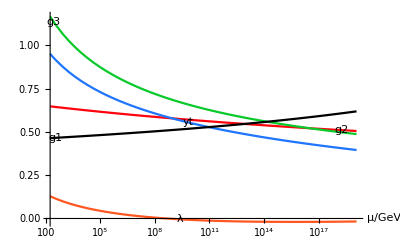

——————————————————————————————————————————————————

```mathematica
run[thresholds,variables,"down","SM",printOut->True,MaxSteps->10^4,WorkingPrecision->MachinePrecision];
```

```mathematica
(*Here we define the appropriate Δλ as a function of the RG scale 'x'. g1 already has the appropriate GUT normalization (g1 = Sqrt[5/3]g )*)
```

```mathematica
Δλonetwo[x_] := 48 π^2(1/g1[x]^2 - 1/g2[x]^2)
Δλtwothree[x_] := 48 π^2(1/g2[x]^2 - 1/g3[x]^2)
```

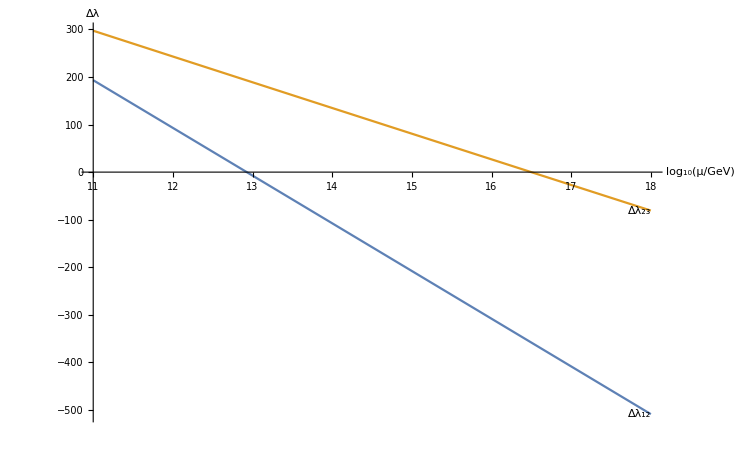

```mathematica
Plot[{Δλonetwo[10^logx],Δλtwothree[10^logx]}, {logx,11,18}, AxesLabel->{"log_10(μ/GeV)",Δλ}, PlotLabels->Placed[{"Δλ_12","Δλ_23"},{Scaled[1],Before}]]
```

```mathematica
(*Calculate delta lambda values from 14 - 17 *)
```

```mathematica
x = {14,14.5,15,15.5,16,16.5,17}
```

```mathematica
onetwoarray = {}
twothreearray = {}
For[i=1,i<8,i++,
AppendTo[onetwoarray, Δλonetwo[10^x[[i]]]];
AppendTo[twothreearray, Δλtwothree[10^x[[i]]]]
]
onetwoarray
twothreearray
```

{-107.609,-157.762,-207.919,-258.078,-308.24,-358.404,-408.571}

{134.802,107.787,80.7879,53.8046,26.8361,-0.118745,-27.0608}

```mathematica
(*Calculate delta lambda values from 10 - 18 *)
```

```mathematica
onetwoarray = {Δλonetwo[10^10], Δλonetwo[10^11],Δλonetwo[10^12],Δλonetwo[10^13],Δλonetwo[10^14],Δλonetwo[10^15], Δλonetwo[10^16], Δλonetwo[10^17], Δλonetwo[10^18]}
twothreearray =  {Δλtwothree[10^10], Δλtwothree[10^11],Δλtwothree[10^12],Δλtwothree[10^13],Δλtwothree[10^14],Δλtwothree[10^15], Δλtwothree[10^16], Δλtwothree[10^17], Δλtwothree[10^18]}
```

{293.51,193.251,92.977,-7.30987,-107.609,-207.919,-308.24,-408.571,-508.912}

{351.668,297.305,243.049,188.885,134.802,80.7879,26.8361,-27.0608,-80.9081}